# What shall we do with the drunken sailor?

## Jon McLoone

Back in 1988 when Mathematica was just a year old, and no-one in my university had heard of it, I was forced to learn FORTRAN. 

My end of term project was this problem: “A drunken sailor returns to his ship via a plank 15 paces long and 7 paces wide. With each step he has equal chance of stepping forward, left, right, or standing still. What is the probability that he returns safely to his ship?”. I wrote a page or so of ugly code, passed the course and never wrote FORTAN again. Today I thought I would revisit the problem.

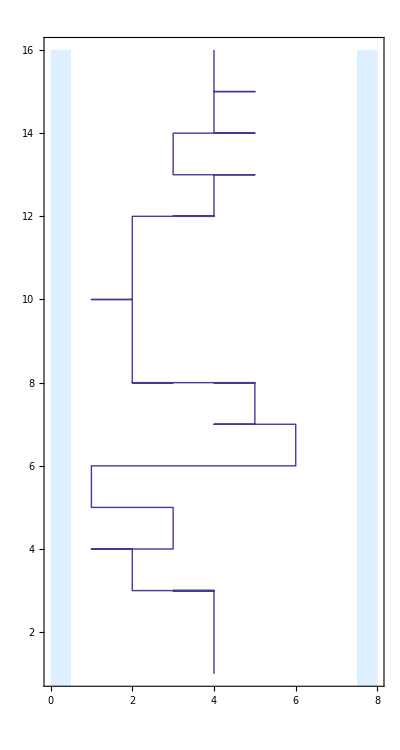

We can code the logic of his walk quite easily using separate rules for each case. Firstly, if he is ever on the 16th step or already on the ship then he is automatically on the ship next time.

```mathematica
step[{x_,16}|Ship]:=Ship;
```

If he is ever out-of bounds of the plank, at position 0 or 8, then he falls in the water, and stays there

```mathematica
step[{0,y_}|{8,y_}|Splash]:=Splash;
```

And finally all other cases, he steps to one of four new positions.

```mathematica
step[{x_,y_}]:=RandomChoice[{{x,y},{x+1,y},{x-1,y},{x,y+1}}];
```

To simulate an entire journey we repeatedly step until he reaches one of then named locations, then return that location.

```mathematica
simulation[start_List]:=Block[{pos=start},While[Head[pos]===List,pos=step[pos]];pos]
```

Now we can run that simulation, I am going to generously assume that the concierge of the Monte Carlo casino, where he has been drinking all night, places him in the middle of the end of the plank before leaving him.

```mathematica
simulation[{4,1}]
```

Splash

Using FixedPointList instead of While gives a neat way to visualize his stagger.

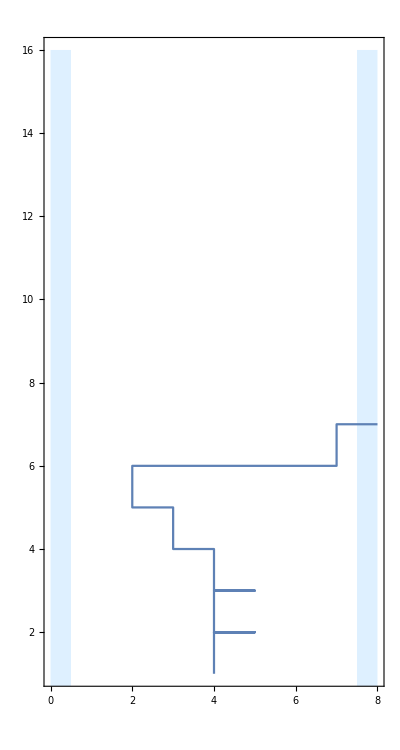

```mathematica
ListPlot[FixedPointList[step,{4,1},SameTest->(#1===#2&&Head[#1]===Symbol&)],
Joined->True,AspectRatio->15/8,Frame->True,PlotRange->{{0,8},{1,16}},
Prolog->{LightBlue,Rectangle[{0,0},{0.5,16}],Rectangle[{7.5,0},{8,16}]}]
```

Now all we need to do is to run the simulation lots of times and count the successes vs the fails

```mathematica
Tally[Table[simulation[{4,1}],{100000}]]
```

{{Splash,84889},{Ship,15111}}

This gives us about 18 % chance of success and took only 5 lines of code.

Because of the discrete state nature of the problem there is another way to look at it that efficiently gives us the probability not only of this journey, but the chances of getting from any one place to any other place in any specific number of steps, and that is to use Markov Chains. I didn’t know anything about Markov Chains in 1988, so I have no idea how much work it would have been in FORTRAN, but here is how you might do it in Mathematica.

First we number all of the positions. In the 15×7 problem there are 105 possible places to stand on the plank. I will designate the water as position 106 and ship as 107 (or more generally water is width × height+1 and ship as width × height+2). Now we construct a matrix to represent all the transition probabilities. For example since the chances of moving from position 1 to position 2 is 1/4 then M_(1,2)=1/4 etc. If you do this right, every row of the transition matrix sums to 1 since there is 100% probability that you go to some state. This is the trickiest part of the problem, but fortunately SparseArray has a rather neat pattern specification that allows us to describe all of the values in a few lines.

```mathematica
transitionProbabilityMatrix[width_,length_]:=
	With[{splash=width ×length+1,home=width ×length+2},
		SparseArray[{
			{splash,splash}→1,(*Wet sailor stays wet*)
			{home,home}→1, (*Once home he stays safe*)
			{home|splash,_}→0,(*No chance of reaching any other point from either home or water*)
			{x_,x_}→1/4, (*Chance of staying put*)
			{pos_/;width×(length-1)<pos≤width×length,home}→1/4,(*Chance of getting home from final row*)
			{pos_/;(Mod[pos,width]==1||Mod[pos,width]==0),splash}→1/4,(*Chance of splash from edge of plank*)
			{pos1_,pos2_}/;(pos2-pos1===1&&Mod[pos1,width]=!=0)→1/4,(*Chance of right step when not on right edge of plank*)
			{pos1_,pos2_}/;(pos2-pos1===-1&&Mod[pos1,width]=!=1)→1/4,(*Chance of left step when not on left edge of plank*)
			{pos1_,pos2_}/;pos2-pos1===width→1/4},(*Chance of stepping forward*)
			{width × length+2,width ×length+2}
		]
	];
```

Here for example is the transition matrix for a small 3×3 plank

```mathematica
transitionProbabilityMatrix[3,3]//MatrixForm
```

(1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0
1/4 | 1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 1/4 | 0 | 0 | 1/4 | 0 | 0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 0 | 1/4 | 1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 1/4 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 1/4 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

And here is the transition matrix for our larger problem

```mathematica
ArrayPlot[transitionProbabilityMatrix[7,15]]
```

-Graphics-

Here is the first row describing the possible transitions from position 1 (the left hand edge of the start of the plank). It shows equal chances of going to position 1 (standing still), 2 (stepping right), 8 (stepping forward) and 106 (splash).

```mathematica
transitionProbabilityMatrix[7,15][[1]]//Normal
```

{1/4,1/4,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0}

The important thing about doing this is that the MatrixPower[Matrix,n] represents the transition probability matrix for each start position to end position after exactly n steps. So for example here are the probabilities for where you will find the sailor who started in the middle of the plank after 6 steps, showing a 23/512 chance (position -2) of being swimming already

```mathematica
MatrixPower[transitionProbabilityMatrix[7,15],6][[4]]//Normal
```

{11/1024,89/4096,63/2048,141/4096,63/2048,89/4096,11/1024,21/1024,45/1024,135/2048,153/2048,135/2048,45/1024,21/1024,15/1024,75/2048,15/256,285/4096,15/256,75/2048,15/1024,5/1024,15/1024,15/512,35/1024,15/512,15/1024,5/1024,0,15/4096,15/2048,45/4096,15/2048,15/4096,0,0,0,3/2048,3/2048,3/2048,0,0,0,0,0,1/4096,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,23/512,0}

This manipulate lets you visualize his probably (still on the plank) position, along with numeric values of his probability of reaching each destination.

```mathematica
Manipulate[Block[{soln=MatrixPower[N@transitionProbabilityMatrix[7,15],steps][[start]]},
MatrixPlot[Partition[soln,7],PlotLabel→Grid[{
{"Drowned: ",soln[[-2]]},
{"Home: ",soln[[-1]]},
{"Walking: ",Total[soln[[;;-3]]]}}]]],
{{start,4},1,7,1,Appearance→"Labeled"},
{steps,1,100,1,Appearance→"Labeled"},SaveDefinitions→True]
```

So now if we find lim_(x→∞) M^x as x→∞ then we have the probability that he will make it at some point. I am just going to assume that if he hasn’t made it in 1,000 steps then he will probably fall asleep on the plank anyway! So here are the probabilities that he is swimming or home after 1000 steps...

```mathematica
MatrixPower[N@transitionProbabilityMatrix[7,15],1000][[4,-2;;]]//Normal
```

{0.849989,0.150011}

Modelling drunken swimming is a harder problem which I may revisit when Mathematica can do CFD.